# Setup

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Miguel\Github\quantum_chaotic_channels\MG files\LMG chain

```mathematica
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\QMB.wl"]
Get["C:\\Users\\Miguel\\Github\\quantum_chaotic_channels\\Mathematica_packages\\Chaometer.wl"]
```

```mathematica
KroneckerVectorProduct[a_,b_]:=Flatten[KroneckerProduct[a,b]];
BlochVector[ρ_]:=Tr[Pauli[#].ρ]&/@Range[3];
Parity[ψ_,L_]:=ψ[[FromDigits[Reverse[#],2]+1&/@Tuples[{0,1},L]]];
Braket[a_,b_]:=Conjugate[a].b;
MeanLevelSpacingRatio[eigenvalues_]:=Mean[Min/@Transpose[{#,1/#}]&[Ratios[Differences[eigenvalues]]]];
Clear[SurvivalProbability];
SurvivalProbability[ψt_,ψ0_]:=Abs[Braket[ψ0,ψt]]^2;
```

```mathematica
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.07],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];
plotsphere2=Graphics3D[{Opacity[0.3],Sphere[{0,0,0},1]}];
Clear[rho];
rho[vec_]:={{vec[[1]],vec[[2]]},{vec[[3]],vec[[4]]}};
```

```mathematica
LaunchKernels[14]
```

{Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14),Local (14)}

# LMG

## Definitions

```mathematica
(*Operadores*)
Clear[Sz,SM,Sm,Sx,Sy,Qp,Q,P];
Sz[J_]:=DiagonalMatrix[Table[-J+k-1,{k,1,2J+1}]];
SM[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i+1)],{i,-J,J-1}],1];
Sm[J_]:=DiagonalMatrix[Table[Sqrt[J(J+1)-i(i-1)],{i,-J+1,J}],-1];
Sx[J_]:=(1/2)(SM[J]+Sm[J]);
Sy[J_]:=Sy[J]=(1/(2I))(SM[J]-Sm[J]);
Qp[J_]:=DiagonalMatrix[Table[Sqrt[i/2],{i,IntegerPart[2J]}],-1];
Q[J_]:=Qp[J]+Transpose[Qp[J]];
P[J_]:=-I(Qp[J]-Transpose[Qp[J]]);
Clear[H];
H[J_,α_,k_]:=N[(k/(2J))(Sx[J].Sx[J])+(α)(Sz[J])];

(*Coherent states*)
Clear[z];
z[J_,Q_,P_]:=Module[{alfa1=(Q+I*P)/Sqrt[4-(Q^2+P^2)]},
Normalize[N[Table[If[alfa1==0&&i==-J,1,Sqrt[Binomial[2J,J+i]]*Exp[(J+i)Log[alfa1]]],{i,-J,J}],20]]
];

(*Stuff to partition the system*)
Clear[CG];
CG[n1_,n_,N1_,N2_]:=CG[n1,n,N1,N2]=Binomial[N1,n1]*Binomial[N2,n-n1]/Binomial[N1+N2,n];
Clear[bloch];
bloch[rho_]:={2Re[rho[[1,2]]],-2Im[rho[[1,2]]],rho[[1,1]]-rho[[2,2]]};
(*Plot Bloch sphere with Bloch vector*)
plotsphere=SphericalPlot3D[1,{theta,0,Pi},{phi,0,2 Pi},PlotStyle->Opacity[0.1],PlotRange->{{-1,1},{-1,1},{-1,1}},Boxed->False,Axes->False];

Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(Exp[-I*n*neweigenval]).Abs[ini]^2]^2
];
```

## Hamiltonian

## Hamiltonian

```mathematica
J=100;
α=0.84;
k=-2;
```

```mathematica
Clear[mat,neweigenvec];
mat=H[J,α,k];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Transpose[Sort[Transpose[Eigensystem[matM]]]];
{eigenvalm,eigenvecm}=Transpose[Sort[Transpose[Eigensystem[matm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
iprs=ParallelTable[Total[Quiet[Abs[i]^4]],{i,neweigenvec}];
```

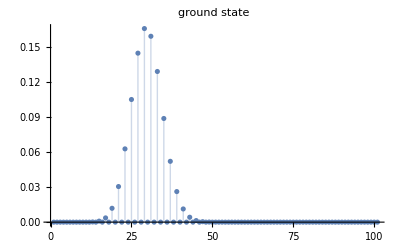

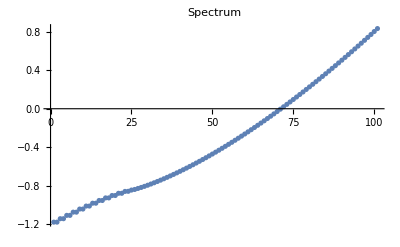

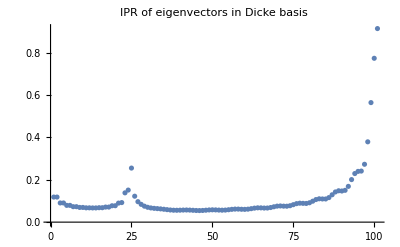

```mathematica
ListPlot[Quiet[Abs[neweigenvec[[1]]]^2],PlotRange->All,Filling->Axis,PlotLabel->Style["ground state",25,Black]]
ListPlot[neweigenval/J,PlotRange->All,PlotLabel->Style["Spectrum",25,Black]]
ListPlot[iprs,PlotRange->All, PlotLabel->Style["IPR of eigenvectors in Dicke basis",20,Black]]
```

### Initial conditions (Q,P) = (1,1)

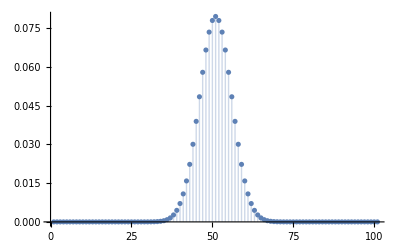

```mathematica
{Q,P}={1,1};
ini=z[J,Q,P];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis]
```

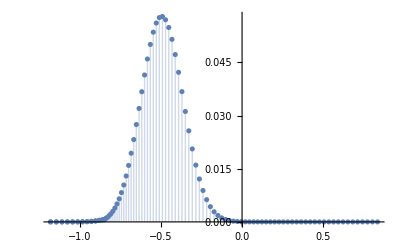

```mathematica
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
ListPlot[Transpose[{neweigenval/J,Quiet[Abs[inilmg]^2]}],PlotRange->All,Filling->Axis]
```

```mathematica
Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(Exp[-I*n*neweigenval]).Abs[ini]^2]^2
];
```

```mathematica
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
data=ParallelTable[sur[inilmg,t],{t,tlist}];
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
```

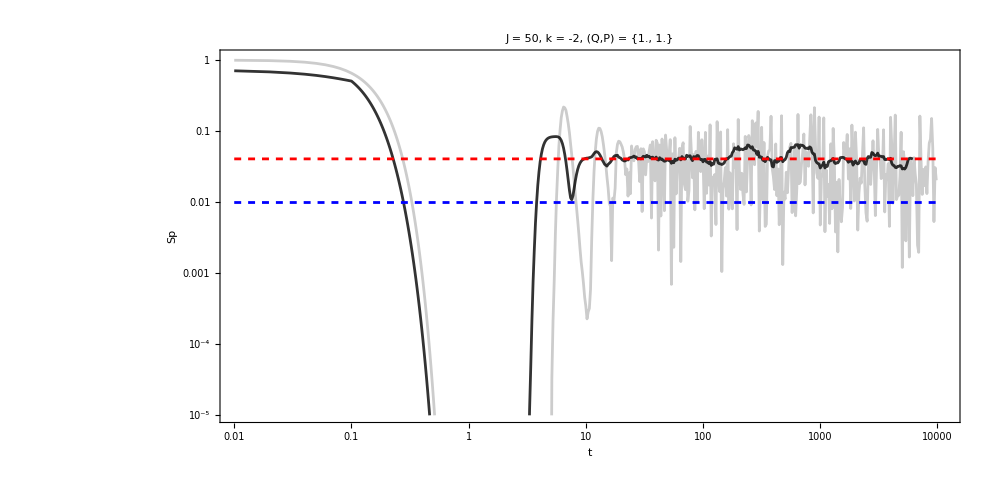

```mathematica
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1/2,ImageSize->1000],plot2}]
```

### Initial conditions (Q,P) = (0,0)

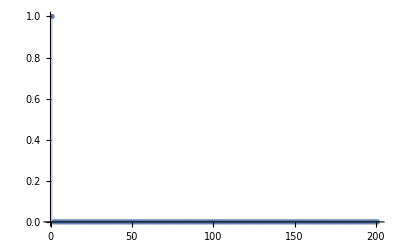

```mathematica
{Q,P}={0,0};
ini=z[J,Q,P];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis]
```

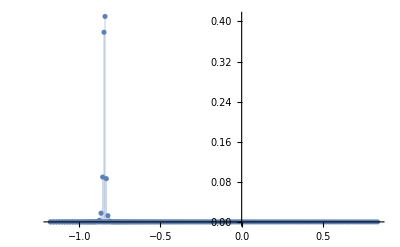

```mathematica
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
ListPlot[Transpose[{neweigenval/J,Quiet[Abs[inilmg]^2]}],PlotRange->All,Filling->Axis]
```

```mathematica
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
data=ParallelTable[sur[inilmg,t],{t,tlist}];
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
```

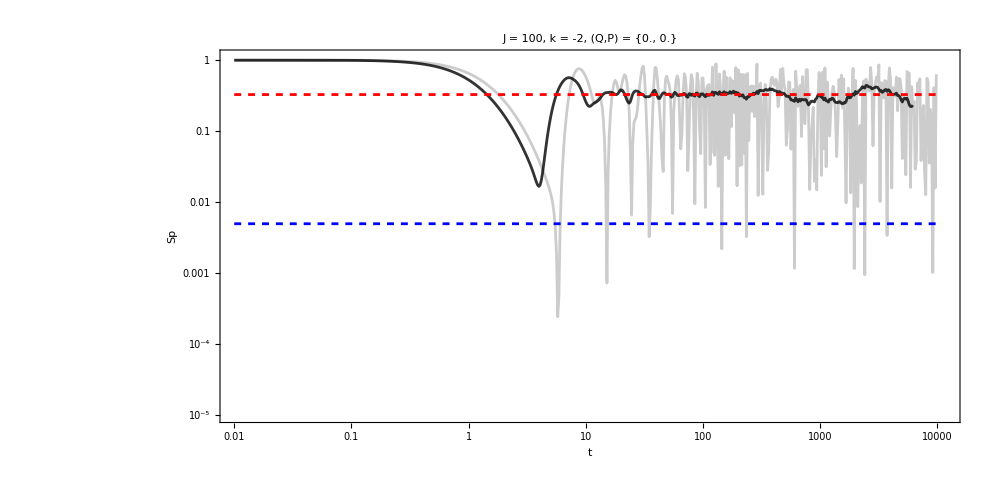

```mathematica
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1/2,ImageSize->1000],plot2}]
```

### Initial conditions (Q,P) = (1.999,0)

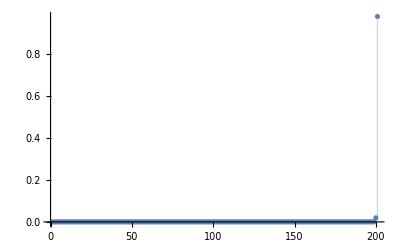

```mathematica
{Q,P}={1.9999,0};
ini=Quiet[z[J,Q,P]];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis]
```

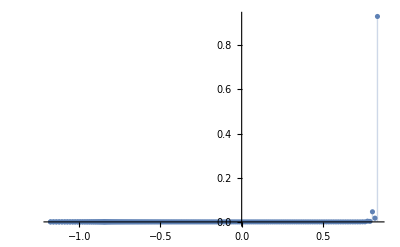

```mathematica
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
ListPlot[Transpose[{neweigenval/J,Quiet[Abs[inilmg]^2]}],PlotRange->All,Filling->Axis]
```

```mathematica
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,4},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
```

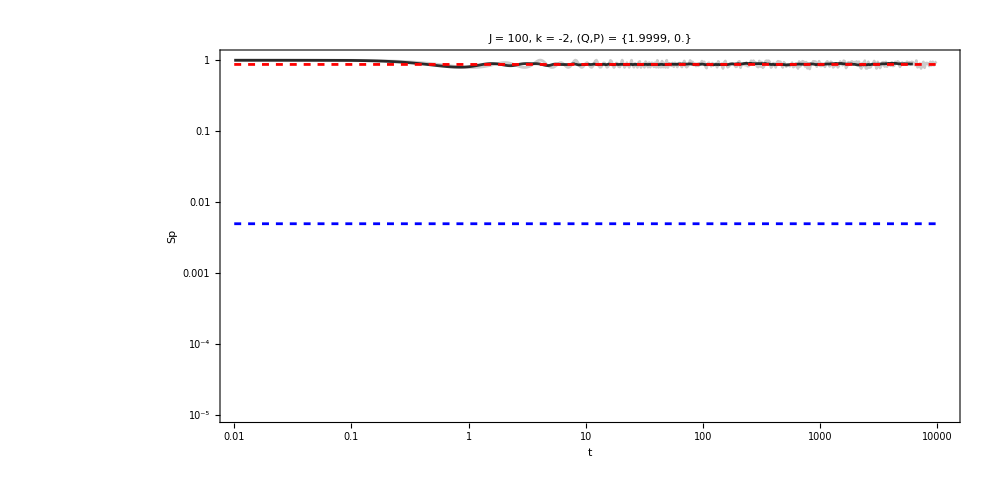

```mathematica
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1/2,ImageSize->1000],plot2}]
```

## Reduced density matrix (Q,P) = (1,1)

```mathematica
{Q,P}={0.5,0.5};
ini=z[J,Q,P];
```

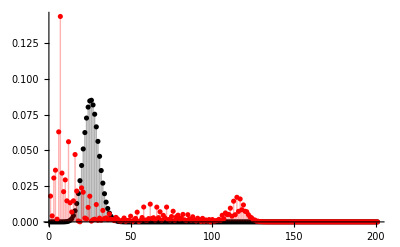

```mathematica
tf=1000;
ψt=StateEvolution[tf,ini,neweigenval,neweigenvec];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis,PlotStyle->Black];
laterprofile=ListPlot[Quiet[Abs[ψt]^2],PlotRange->All,Filling->Axis,PlotStyle->Red];
Show[{iniprofile,laterprofile},ImageSize->400,PlotRange->All]
```

```mathematica
newtlist=Range[0,1000];
ψts=ParallelTable[StateEvolution[t,ini,neweigenval,neweigenvec],{t,newtlist}];
```

```mathematica
Clear[J,N1,N2];
J=100;
N1=1; (*Here, I'm partitioning the system of N=2J=200 spins in subsystem N1 with 1 spin and N2 with 199 spins*)
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
rhos={};
Do[
b=ψts[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[ψts]}];
```

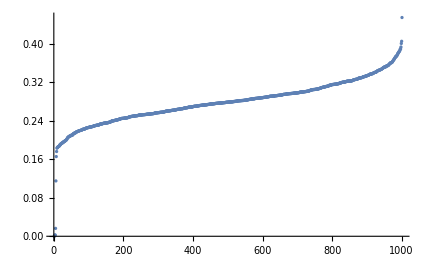

```mathematica
linearentropya=ListPlot[Sort[Table[1-Chop[Tr[i.i]],{i,rhos}]],PlotRange->All]
```

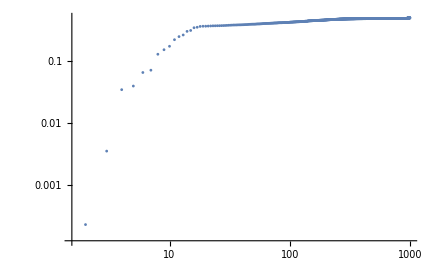

```mathematica
linearentropya=ListLogLogPlot[Sort[Table[1-Chop[Tr[i.i]],{i,rhos}]],PlotRange->All]
```

### Bloch Plots

```mathematica
ColorData["Rainbow"]
```

ColorDataFunction[…]

```mathematica
blochs[[2;;-1]]//Dimensions
```

{1000,3}

```mathematica
RGBColor[0.5,0.5,0.5]
```

```mathematica
colordata=Table[{RGBColor[1-i,0.3,i/Length[blochs[[2;;-1]]]]},{i,Length[blochs[[2;;-1]]]}];
```

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=ListPointPlot3D[blochs[[2;;-1]],PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[{plotpuntos,plotpuntosini},plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

## Reduced density matrix (Q,P) = (0,0)

```mathematica
{Q,P}={0,0};
ini=z[J,Q,P];
```

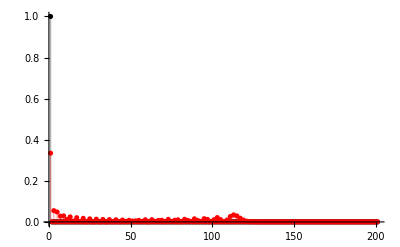

```mathematica
tf=1000;
ψt=StateEvolution[tf,ini,neweigenval,neweigenvec];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis,PlotStyle->Black];
laterprofile=ListPlot[Quiet[Abs[ψt]^2],PlotRange->All,Filling->Axis,PlotStyle->Red];
Show[{iniprofile,laterprofile},ImageSize->400,PlotRange->All]
```

```mathematica
newtlist=N[Range[0,1000]];
ψts=ParallelTable[StateEvolution[t,ini,neweigenval,neweigenvec],{t,newtlist}];
```

```mathematica
Clear[J,N1,N2];
J=100;
N1=1; (*Here, I'm partitioning the system of N=2J=200 spins in subsystem N1 with 1 spin and N2 with 199 spins*)
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
rhos={};
Do[
b=ψts[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[ψts]}];
```

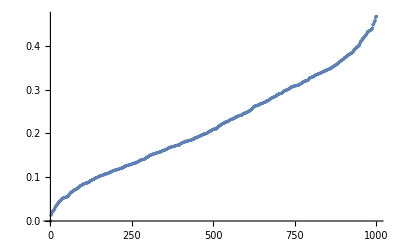

```mathematica
linearentropya=ListPlot[Sort[Table[1-Chop[Tr[i.i]],{i,rhos}]],PlotRange->All]
```

### Bloch Plots

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=ListPointPlot3D[blochs[[2;;-1]][[-100;;-1]],ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[{plotpuntos,plotpuntosini},plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

## Reduced density matrix (Q,P) = (1.999,0)

```mathematica
{Q,P}={1.999,0};
ini=z[J,Q,P];
```

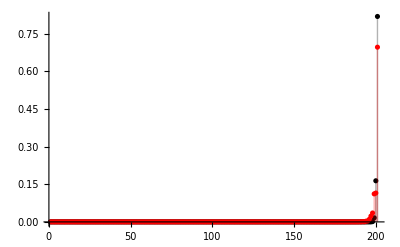

```mathematica
tf=1000;
ψt=StateEvolution[tf,ini,neweigenval,neweigenvec];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis,PlotStyle->Black];
laterprofile=ListPlot[Quiet[Abs[ψt]^2],PlotRange->All,Filling->Axis,PlotStyle->Red];
Show[{iniprofile,laterprofile},ImageSize->400,PlotRange->All]
```

```mathematica
newtlist=N[Range[0,1000]];
ψts=ParallelTable[StateEvolution[t,ini,neweigenval,neweigenvec],{t,newtlist}];
```

```mathematica
Clear[J,N1,N2];
J=100;
N1=1; (*Here, I'm partitioning the system of N=2J=200 spins in subsystem N1 with 1 spin and N2 with 199 spins*)
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
rhos={};
Do[
b=ψts[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[ψts]}];
```

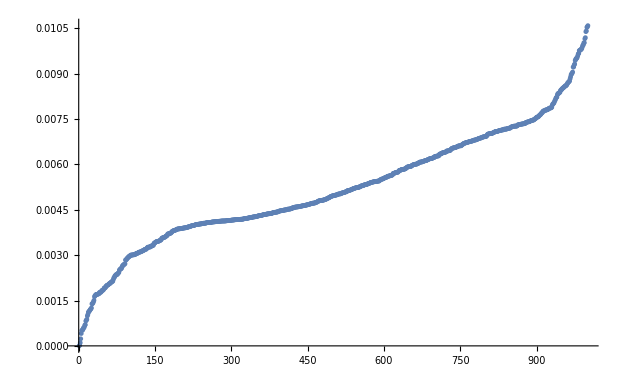

```mathematica
linearentropya=ListPlot[Sort[Table[1-Chop[Tr[i.i]],{i,rhos}]],PlotRange->All]
```

### Bloch Plots

```mathematica
blochs=Table[bloch[i],{i,rhos}];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=ListPointPlot3D[blochs[[2;;-1]],ColorFunction->"Rainbow",PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
Show[{plotpuntos,plotpuntosini},plotsphere,ImageSize->400,PlotLabel->Style["k = "<>ToString[N[k]]<>", N = "<>ToString[J]<>", n1 = "<>ToString[N1],25,Black]]
```

-Graphics3D-

## Energy surface

```mathematica
Clear[h2M,h2m];
(*h2M[α_,k_,Q_,P_]:=α((1/2)((Q-0.20)^2+P^2)-1)+(k*(Q-0.20)^2)(1-(1/4)((Q-0.20)^2+P^2));*)
h2M[α_,k_,Q_,P_]:=α((1/2)(Q^2+P^2)-1)+(k*Q^2)(1-(1/4)(Q^2+P^2));
```

```mathematica
Clear[α,k];
α=0.84;
k=-2;
Plot3D[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],23,Black],ColorFunction->"WatermelonColors",PlotLegends->Automatic]
```

-Graphics3D-

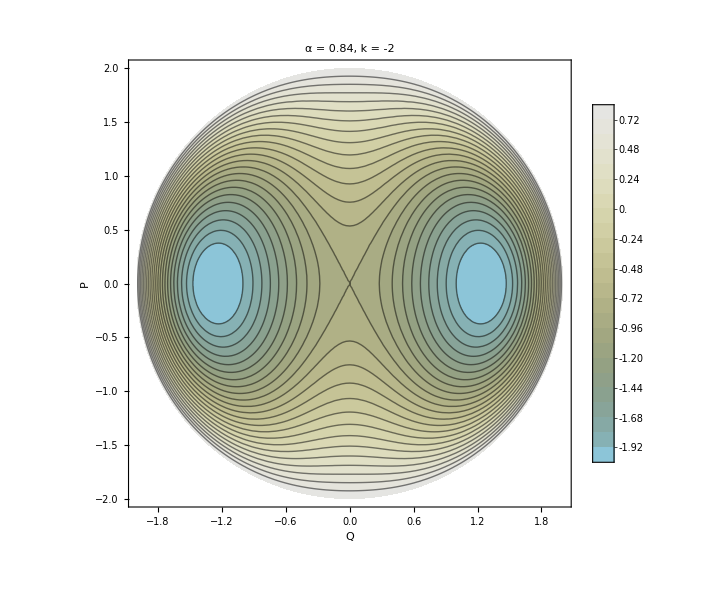

```mathematica
surface=ContourPlot[h2M[α,k,Q,P],{Q,P}∈Disk[{0,0},1.999],PlotRange->All,PlotTheme->"Detailed",PerformanceGoal->"Quality",PlotLabel->Style["α = "<>ToString[α]<>", k = "<>ToString[k],50,Black],Contours->100,FrameLabel->{Style["Q",40,Black],Rotate[Style["P",40,Black],-90Degree]},LabelStyle->Directive[ 30,Black],AspectRatio->1,Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->True,ImageSize->600,GridLines->None,ColorFunction->"LightTerrain"]
```

## Survival

```mathematica
α=0.84;
k=-2;
```

```mathematica
J=1000;
Clear[mat,neweigenvec];
mat=H[J,α,k];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Transpose[Sort[Transpose[Eigensystem[matM]]]];
{eigenvalm,eigenvecm}=Transpose[Sort[Transpose[Eigensystem[matm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
{Q,P}={1,1};
ini=z[J,Q,P];
inilmg=Conjugate[neweigenvec].ini;
```

```mathematica
ListPlot[{Quiet[Abs[ini]^2],Quiet[Abs[inilmg]^2]},PlotRange->All,Filling->Axis,PlotStyle->{Gray,Red}]
```

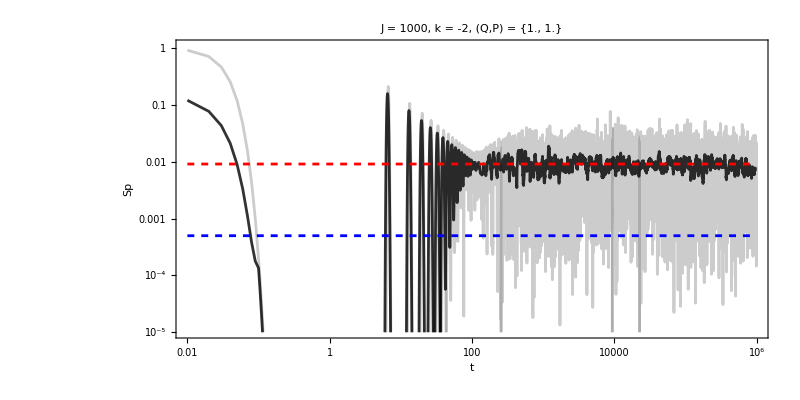

```mathematica
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=5000;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,6.5},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
```

```mathematica
newdata=ParallelTable[{t,sur[inilmg,t]},{t,Range[0,1000,0.1]}];
```

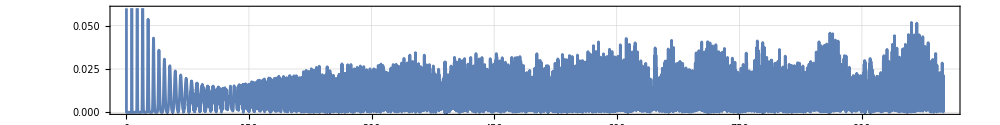

```mathematica
ListPlot[newdata,Joined->True,PlotTheme->"Detailed",ImageSize->1000,PlotRange->{All,{0,0.06}},AspectRatio->1/8]
```

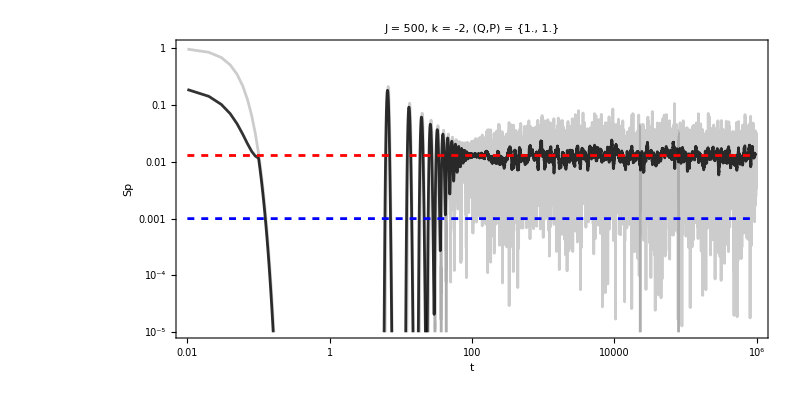

```mathematica
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=5000;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,6.5},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
```

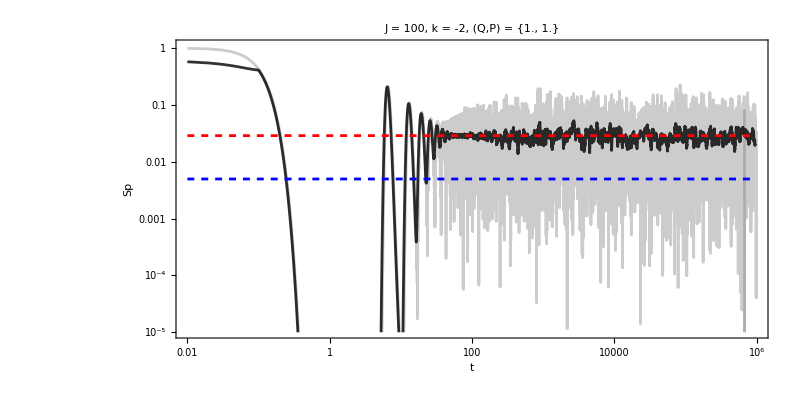

```mathematica
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=5000;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,6.5},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
```

## Reduced density matrix for all initial conditions

## Reduced density matrix (Q,P)

```mathematica
J=50;
α=0.84;
k=-2;
Clear[mat,neweigenvec];
mat=H[J,α,k];
matM=Table[mat[[i,j]],{i,1,2J+1,2},{j,1,2J+1,2}];
matm=Table[mat[[i,j]],{i,2,2J+1,2},{j,2,2J+1,2}];
{eigenvalM,eigenvecM}=Transpose[Sort[Transpose[Eigensystem[matM]]]];
{eigenvalm,eigenvecm}=Transpose[Sort[Transpose[Eigensystem[matm]]]];
zerosM=Table[0,{i,J}];
zerosm=Table[0,{i,J+1}];
neweigenvecM=Table[Riffle[eigenvecM[[j]],zerosM],{j,J+1}];
neweigenvecm=Table[Riffle[zerosm,eigenvecm[[j]]],{j,J}];
neweigenvec=Riffle[neweigenvecM,neweigenvecm];
neweigenval=Riffle[eigenvalM,eigenvalm];
iprs=ParallelTable[Total[Quiet[Abs[i]^4]],{i,neweigenvec}];
```

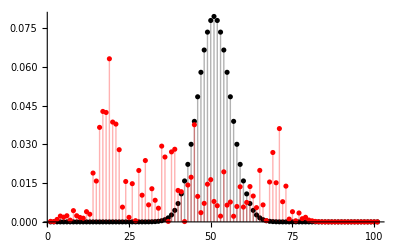

```mathematica
{Q,P}={1,1};
ini=z[J,Q,P];
tf=600;
ψt=StateEvolution[tf,ini,neweigenval,neweigenvec];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis,PlotStyle->Black];
laterprofile=ListPlot[Quiet[Abs[ψt]^2],PlotRange->All,Filling->Axis,PlotStyle->Red];
Show[{iniprofile,laterprofile},ImageSize->400,PlotRange->All]
```

```mathematica
newtlist=Range[100,tf];
ψts=ParallelTable[StateEvolution[t,ini,neweigenval,neweigenvec],{t,newtlist}];
```

```mathematica
Clear[N1,N2];
N1=1; (*Here, I'm partitioning the system of N=2J=200 spins in subsystem N1 with 1 spin and N2 with 199 spins*)
N2=2J-N1;
rhos={};
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
rhos={};
Do[
rho=ConstantArray[0,{N1+1,N1+1}];
b=ψts[[i]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{i,Length[ψts]}];
```

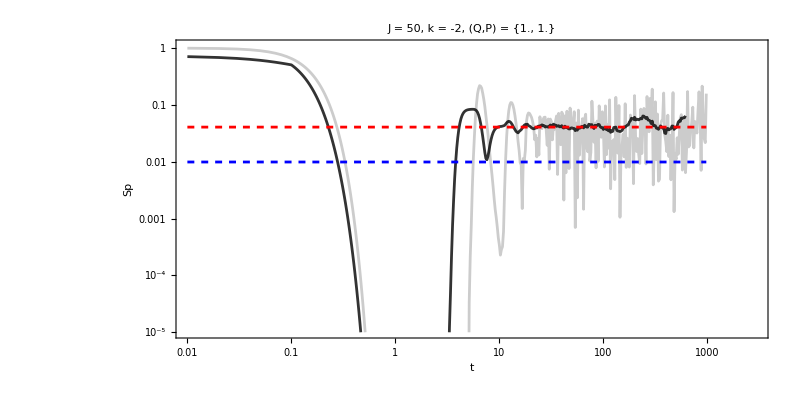

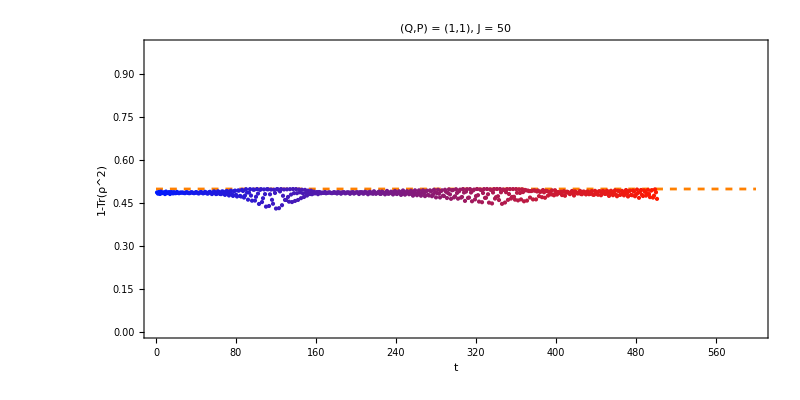

-Graphics3D-

```mathematica
linearentropy=Table[{i,1-Chop[Tr[rhos[[i]]^2]]},{i,Length[rhos]}];
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
blochs=Table[bloch[i],{i,rhos}];
colors1=Table[RGBColor[i/Length[blochs],0.1,1-i/Length[blochs]],{i,Length[blochs]}];
coloredPoints=MapThread[{#2,Point[#1]}&,{linearentropy,colors1}];
limit=Plot[0.5,{x,0,tf},PlotStyle->Directive[Orange,Dashed]];
plot=Graphics[coloredPoints,PlotRange->{All,{0,1}},FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->False,GridLines->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), J = "<>ToString[J],Black,35]];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=Graphics3D[Table[{colors1[[i]],Point[blochs[[i]]]},{i,Length[blochs]}]];
Show[plot,limit]
Show[{plotpuntosini,plotpuntos},plotsphere,ImageSize->600,PlotLabel->Style["(Q,P) = (1,1), System size = "<>ToString[N1]<>" spins",25,Black]]
```

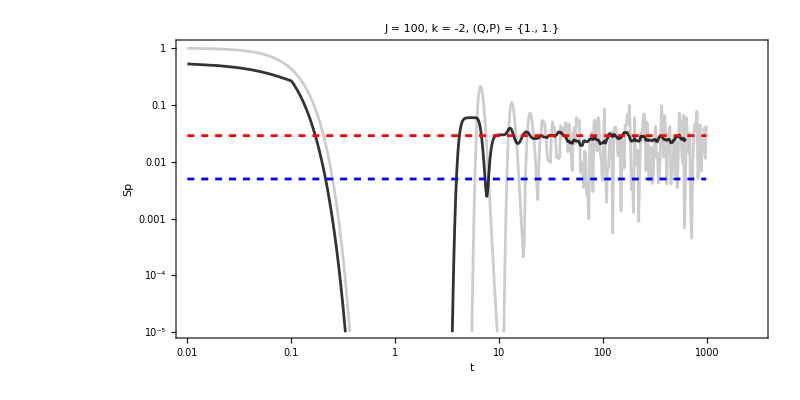

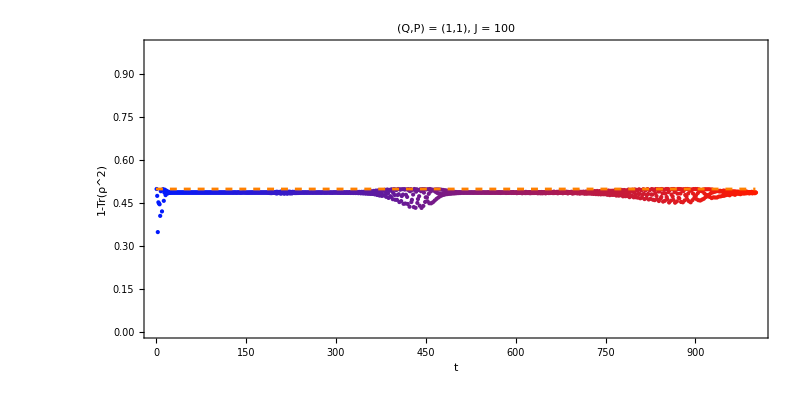

-Graphics3D-

```mathematica
linearentropy=Table[{i,1-Chop[Tr[rhos[[i]]^2]]},{i,Length[rhos]}];
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
blochs=Table[bloch[i],{i,rhos}];
colors1=Table[RGBColor[i/Length[blochs],0.1,1-i/Length[blochs]],{i,Length[blochs]}];
coloredPoints=MapThread[{#2,Point[#1]}&,{linearentropy,colors1}];
limit=Plot[0.5,{x,0,tf},PlotStyle->Directive[Orange,Dashed]];
plot=Graphics[coloredPoints,PlotRange->{All,{0,1}},FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->False,GridLines->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), J = "<>ToString[J],Black,35]];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=Graphics3D[Table[{colors1[[i]],Point[blochs[[i]]]},{i,Length[blochs]}]];
Show[plot,limit]
Show[{plotpuntosini,plotpuntos},plotsphere,ImageSize->600,PlotLabel->Style["(Q,P) = (1,1), System size = "<>ToString[N1]<>" spins",25,Black]]
```

-Graphics-

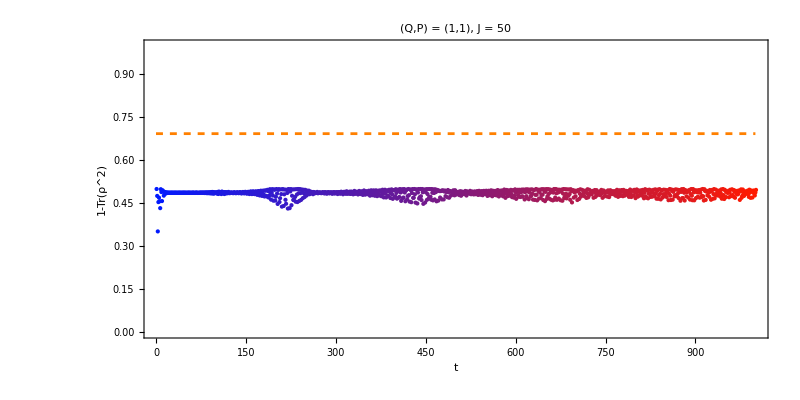

-Graphics3D-

```mathematica
linearentropy=Table[{i,1-Chop[Tr[rhos[[i]]^2]]},{i,Length[rhos]}];
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
blochs=Table[bloch[i],{i,rhos}];
colors1=Table[RGBColor[i/Length[blochs],0.1,1-i/Length[blochs]],{i,Length[blochs]}];
coloredPoints=MapThread[{#2,Point[#1]}&,{linearentropy,colors1}];
limit=Plot[-Log[0.5],{x,0,tf},PlotStyle->Directive[Orange,Dashed]];
plot=Graphics[coloredPoints,PlotRange->{All,{0,1}},FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->False,GridLines->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), J = "<>ToString[J],Black,35]];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=Graphics3D[Table[{colors1[[i]],Point[blochs[[i]]]},{i,Length[blochs]}]];
Show[plot,limit]
Show[{plotpuntosini,plotpuntos},plotsphere,ImageSize->600,PlotLabel->Style["(Q,P) = (1,1), System size = "<>ToString[N1]<>" spins",25,Black]]
```

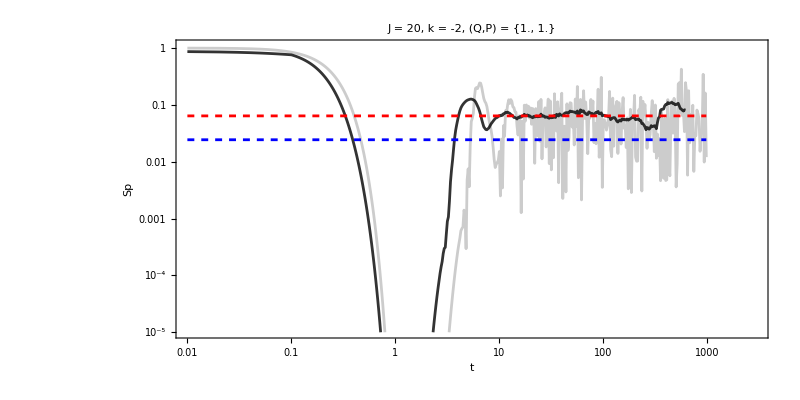

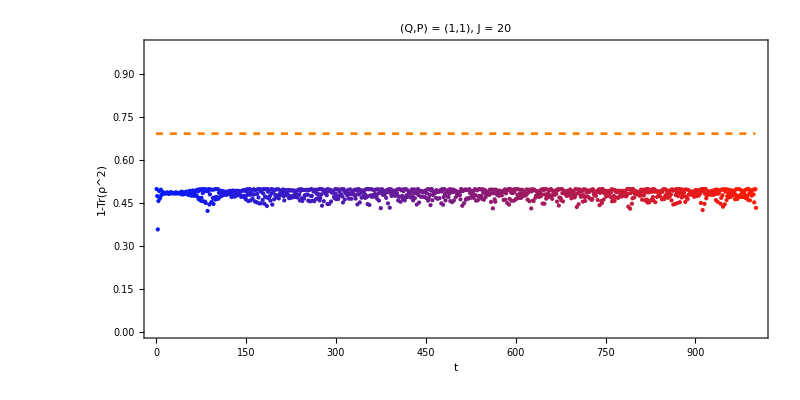

-Graphics3D-

```mathematica
linearentropy=Table[{i,1-Chop[Tr[rhos[[i]]^2]]},{i,Length[rhos]}];
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
blochs=Table[bloch[i],{i,rhos}];
colors1=Table[RGBColor[i/Length[blochs],0.1,1-i/Length[blochs]],{i,Length[blochs]}];
coloredPoints=MapThread[{#2,Point[#1]}&,{linearentropy,colors1}];
limit=Plot[-Log[0.5],{x,0,tf},PlotStyle->Directive[Orange,Dashed]];
plot=Graphics[coloredPoints,PlotRange->{All,{0,1}},FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->False,GridLines->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), J = "<>ToString[J],Black,35]];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=Graphics3D[Table[{colors1[[i]],Point[blochs[[i]]]},{i,Length[blochs]}]];
Show[plot,limit]
Show[{plotpuntosini,plotpuntos},plotsphere,ImageSize->600,PlotLabel->Style["(Q,P) = (1,1), System size = "<>ToString[N1]<>" spins",25,Black]]
```

```mathematica
linearentropy=Table[{i,1-Chop[Tr[rhos[[i]]^2]]},{i,Length[rhos]}];
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
blochs=Table[bloch[i],{i,rhos}];
colors1=Table[RGBColor[i/Length[blochs],0.1,1-i/Length[blochs]],{i,Length[blochs]}];
coloredPoints=MapThread[{#2,Point[#1]}&,{linearentropy,colors1}];
limit=Plot[-Log[0.5],{x,0,tf},PlotStyle->Directive[Orange,Dashed]];
plot=Graphics[coloredPoints,PlotRange->{All,{0,1}},FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Method->{"AxesInFront"->True},Method->{"GridInFront"->True},Frame->True,Axes->False,GridLines->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), J = "<>ToString[J],Black,35]];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=Graphics3D[Table[{colors1[[i]],Point[blochs[[i]]]},{i,Length[blochs]}]];
Show[plot,limit]
Show[{plotpuntosini,plotpuntos},plotsphere,ImageSize->600,PlotLabel->Style["(Q,P) = (1,1), System size = "<>ToString[N1]<>" spins",25,Black]]
```

-Graphics-

-Graphics-

-Graphics3D-

### Initial conditions (Q,P) = (1,1)

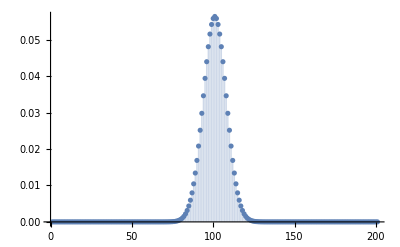

```mathematica
{Q,P}={1,1};
ini=z[J,Q,P];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis]
```

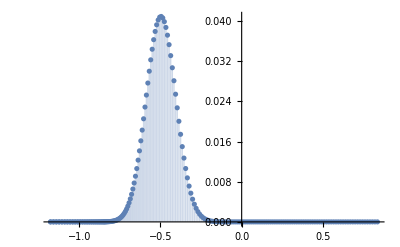

```mathematica
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
ListPlot[Transpose[{neweigenval/J,Quiet[Abs[inilmg]^2]}],PlotRange->All,Filling->Axis]
```

```mathematica
Clear[sur];
sur[ini_,n_]:=Module[{a},
Abs[(Exp[-I*n*neweigenval]).Abs[ini]^2]^2
];
```

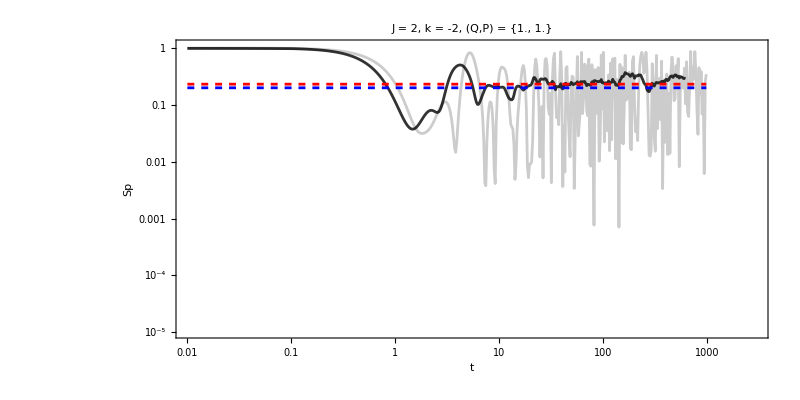

-Graphics-

```mathematica
inilmg=Conjugate[neweigenvec].ini;
ipr=Total[Quiet[Abs[inilmg]^4]];
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
data=ParallelTable[sur[inilmg,t],{t,tlist}];
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
```

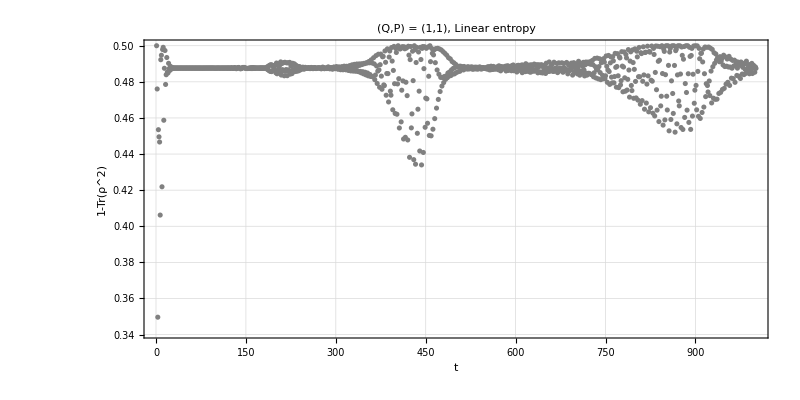

```mathematica
linearentropya=ListPlot[linearentropy,PlotStyle->Gray,FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Frame->True,Axes->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), Linear entropy",25,Black],PlotRange->All,PlotTheme->"Detailed"]
```

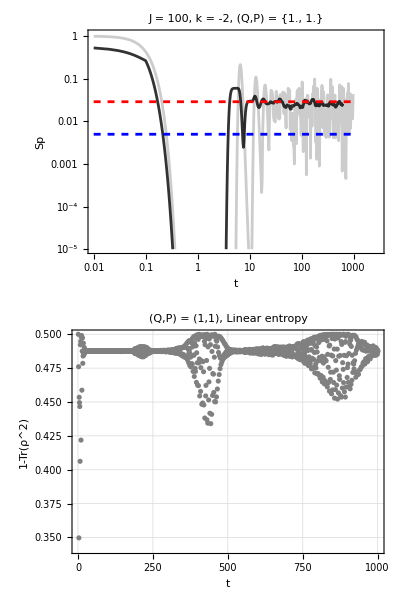

```mathematica
info=Grid[{{plot},{linearentropya}},Spacings->{5,5},Alignment->{Center,Center},Frame->All]
```

```mathematica
Export["info.png",info,ImageResolution->400]
```

info.png

## Reduced density matrix average

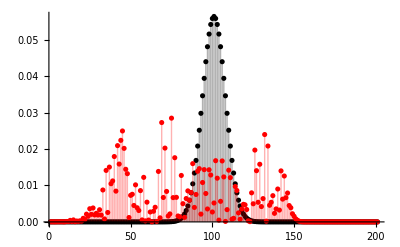

```mathematica
{Q,P}={1,1};
ini=z[J,Q,P];
tf=1000;
newtlist=Range[0,tf];
ψt=StateEvolution[tf,ini,neweigenval,neweigenvec];
iniprofile=ListPlot[Quiet[Abs[ini]^2],PlotRange->All,Filling->Axis,PlotStyle->Black];
laterprofile=ListPlot[Quiet[Abs[ψt]^2],PlotRange->All,Filling->Axis,PlotStyle->Red];
Show[{iniprofile,laterprofile},ImageSize->400,PlotRange->All]
```

```mathematica
ini=ParallelTable[Quiet[z[J,i,0]],{i,0.1,1.9,0.1}];
```

```mathematica
Clear[ψts];
ψts=ParallelTable[StateEvolution[t,j,neweigenval,neweigenvec],{j,ini},{t,newtlist}];
```

```mathematica
Clear[J,N1,N2];
N1=1; (*Here, I'm partitioning the system of N=2J=200 spins in subsystem N1 with 1 spin and N2 with 199 spins*)
N2=2J-N1;
rho=ConstantArray[0,{N1+1,N1+1}];
```

```mathematica
reducedstates={};
Do[
rhos={};
Do[
b=ψts[[k]][[m]];
Do[
rho[[i,j]]=Sum[ b[[i+n2-1]]*Conjugate[b[[j+n2-1]]]*Sqrt[CG[i-1,i+n2-2,N1,N2]*CG[j-1,j+n2-2,N1,N2]],{n2,1,N2+1}];
rho[[j,i]]=Conjugate[rho[[i,j]]];
,{i,1,N1+1},{j,i,N1+1}];
AppendTo[rhos,Chop[rho]];
,{m,Length[newtlist]}];
linearentropy=Table[{l,1-Chop[Tr[rhos[[l]]^2]]},{l,Length[newtlist]}];
AppendTo[reducedstates,linearentropy];
,{k,Length[ini]}];
```

Part::pkspec1: The expression n2 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

$Aborted

```mathematica
colors1=Table[RGBColor[i/(Length[ini]-1),0.1,1-i/(Length[ini]-1)],{i,(Length[ini]-1)}];
```

```mathematica
plota=Table[ListPlot[Join[reducedstates[[1;;2]],reducedstates[[4;;-1]]][[i]],PlotStyle->Directive[colors1[[i]],Opacity[0.25]],FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Frame->True,Axes->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), Linear entropy",25,Black],PlotRange->{All,{0,-Log[0.5]}},PlotTheme->"Detailed",Joined->True],{i,Length[ini]-1}];
plotb=ListPlot[Mean[Join[reducedstates[[1;;2]],reducedstates[[4;;-1]]]],PlotStyle->Directive[Black],FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Frame->True,Axes->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q) = (1,1), Linear entropy",25,Black],PlotRange->{All,{0,-Log[0.5]}},PlotTheme->"Detailed",Joined->True];
```

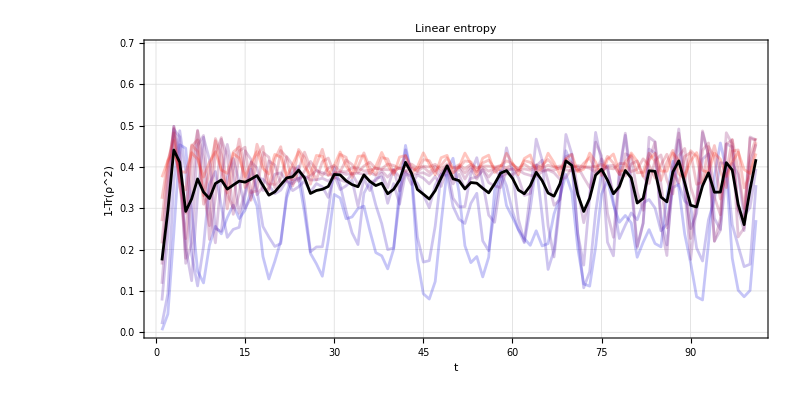

```mathematica
Show[plota,plotb,PlotLabel->Style["Linear entropy",25,Black]]
```

### Bloch Plots

```mathematica
blochs=Table[bloch[i],{i,rhos}];
colors1=Table[RGBColor[i/Length[blochs],0.1,1-i/Length[blochs]],{i,Length[blochs]}];
plotpuntosini=ListPointPlot3D[{blochs[[1]]},PlotStyle->Black,PlotRange->All,AspectRatio->1,PlotTheme->"Detailed",BoxRatios->{1, 1, 1},AxesLabel->{Style["x",Black,25],Style["y",Black,25],Style["z",Black,25]}];
plotpuntos=Graphics3D[Table[{colors1[[i]],Point[blochs[[i]]]},{i,Length[blochs]}]];
Show[{plotpuntosini,plotpuntos},plotsphere,ImageSize->600,PlotLabel->Style["(Q,P) = (1,1), System size = "<>ToString[N1]<>" spins",25,Black]]
```

-Graphics3D-

### Initial conditions (Q,P) = (1,1)

```mathematica
numberOftemporalPoints=500;
tlist=Range[0.01,0.09,0.01]~Join~Flatten[Table[10.^(-5 x/#+i),{i,0,3},{x,#/5,1,-1}]]&[numberOftemporalPoints];
```

```mathematica
data=ParallelTable[sur[inilmg,t],{t,tlist}];
```

```mathematica
Clear[data2,plot,plot2];
data2=Table[Mean[data[[i;;i+20]]],{i,1,Length[data]-20,1}];
```

```mathematica
plot2=LogLogPlot[{ipr,1/(2J+1)},{x,tlist[[1]],tlist[[-1]]},PlotStyle->{{Dashed,Red},{Dashed,Blue}},PlotRange->{{tlist[[1]],tlist[[-1]]},{10^-5,1.1}}];
plot=Show[{ListLogLogPlot[{Transpose[{tlist,data}],Transpose[{tlist[[1;;-21]],data2}]},PlotRange->{{tlist[[1]],tlist[[-1]]+2000},{10^-5,1.1}},PlotTheme->"Detailed",PlotMarkers->False,Joined->True,PlotStyle->{Directive[Gray,Opacity[0.4]],Directive[Black,Opacity[0.8]]},PlotLabel->Row[{Style["J = ",25,Black],Style[J,25,Black],Style[", k = ",25,Black],Style[k,25,Black],Style[", (Q,P) = "<>ToString[N[{Q,P}]]<>"",24,Black]}],FrameLabel->{"t",Rotate["Sp",-90Degree]},LabelStyle->Directive[ 25,Black],AspectRatio->1/2,ImageSize->800],plot2}]
```

-Graphics-

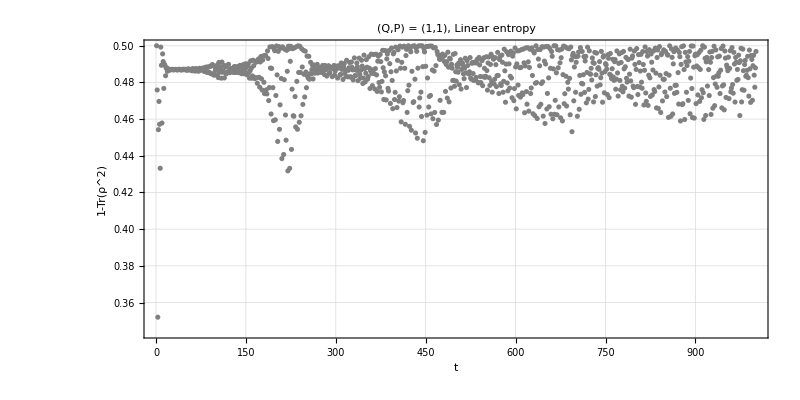

```mathematica
linearentropya=ListPlot[linearentropy,PlotStyle->Gray,FrameLabel->{Style["t",20,Black],Style["1-Tr(ρ^2)",20,Black]},LabelStyle->Directive[ 15,Black],Frame->True,Axes->False,ImageSize->800,AspectRatio->1/2,PlotLabel->Style["(Q,P) = (1,1), Linear entropy",25,Black],PlotRange->All,PlotTheme->"Detailed"]
```

# Quantum map

## LDoS

## Hamiltonian

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
L=10(*number of spins*);
{hx,hz,J}={1,0.8,ConstantArray[1,L-1]};
```

{0.501259,0.520359}

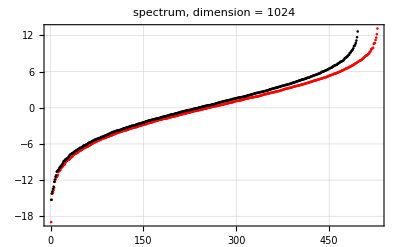

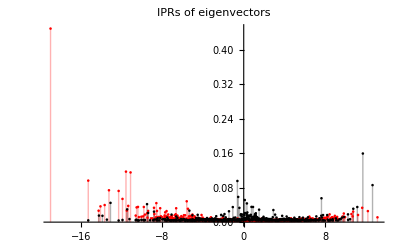

-Graphics-

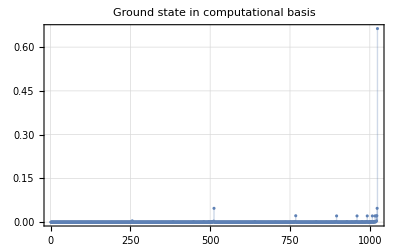

```mathematica
H=IsingNNOpenHamiltonian[hx,hz,J,L];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[H]]]];
{EvenEigVals,evenEigenVecs}={eigVals[[#]],eigVecs[[#]]}&[Flatten[Position[Round[ParallelMap[Braket[#,Parity[#,L]]&,eigVecs],10.^0],1.]]];
OddEigVals=Complement[eigVals,EvenEigVals];
OddEigVecs=Complement[eigVecs,evenEigenVecs];
{MeanLevelSpacingRatio[OddEigVals],MeanLevelSpacingRatio[EvenEigVals]}
ListPlot[{EvenEigVals,OddEigVals},PlotRange->All,PlotTheme->"Detailed",PlotStyle->{Red,Black},ImageSize->400,PlotLabel->Style["spectrum, dimension = "<>ToString[2^L],25,Black]]
iprM=ParallelTable[Total[Quiet[Abs[i]^4]],{i,evenEigenVecs}];
iprm=ParallelTable[Total[Quiet[Abs[i]^4]],{i,OddEigVecs}];
ListPlot[{Transpose[{EvenEigVals,iprM}],Transpose[{OddEigVals,iprm}]},PlotRange->All,Filling->Axis,ImageSize->400,PlotStyle->{Red,Black},PlotLabel->Style["IPRs of eigenvectors",25,Black]]
MatrixPlot[H,PlotRange->All,PlotTheme->"Detailed"]
ListPlot[Abs[eigVecs[[1]]]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->400,PlotLabel->Style["Ground state in computational basis",25,Black]]
```

## Initial state all random

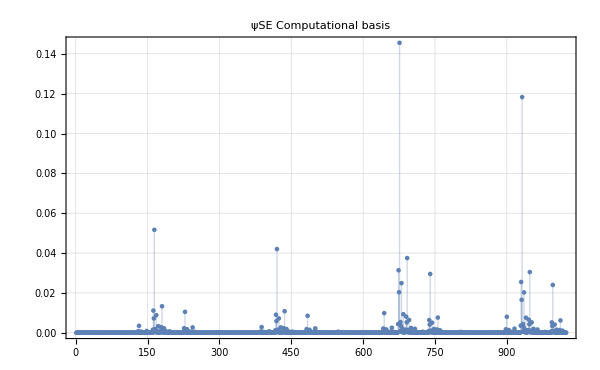
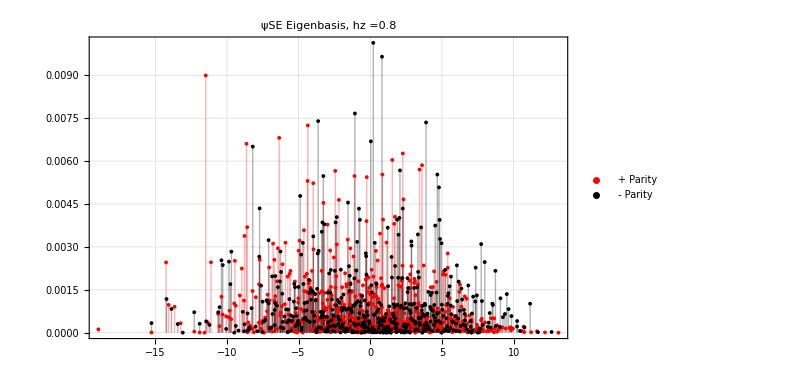

```mathematica
ψ0E=RandomChainProductState[L];
ψ0Espineven=Conjugate[evenEigenVecs].ψ0E;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0E;
plota=ListPlot[Abs[ψ0E]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## Initial state coherent state

```mathematica
Clear[ψ0SE];
a=RandomReal[];
state=qubit[a,a];
ψ0SE=coherentstate[state,L];
a
```

0.901702

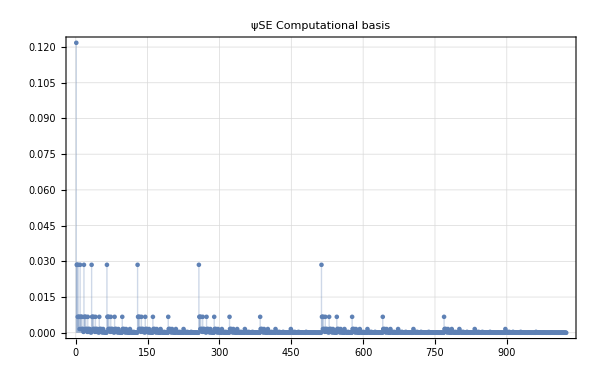
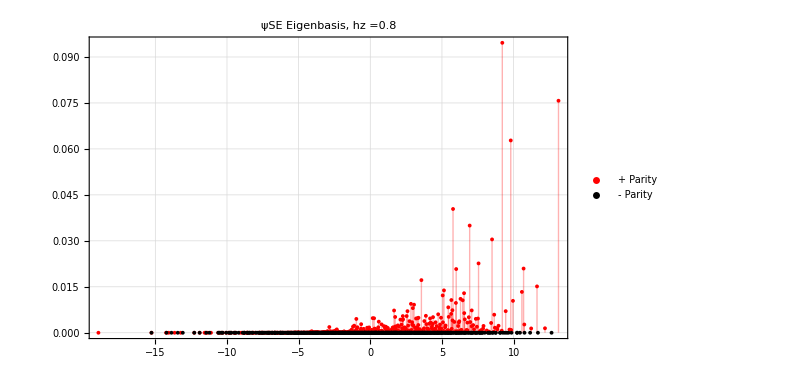

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

```mathematica
Clear[ψ0SE];
state=qubit[Pi/4,Pi/4];
ψ0SE=coherentstate[state,L];
```

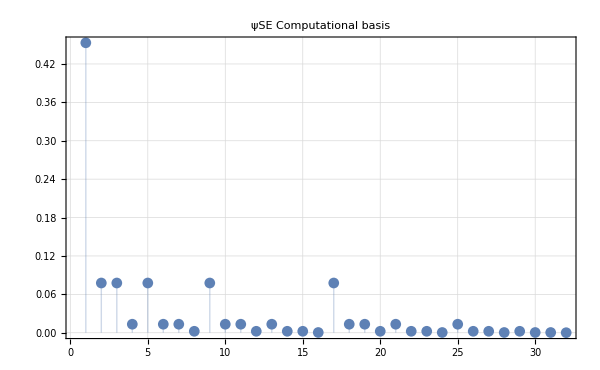
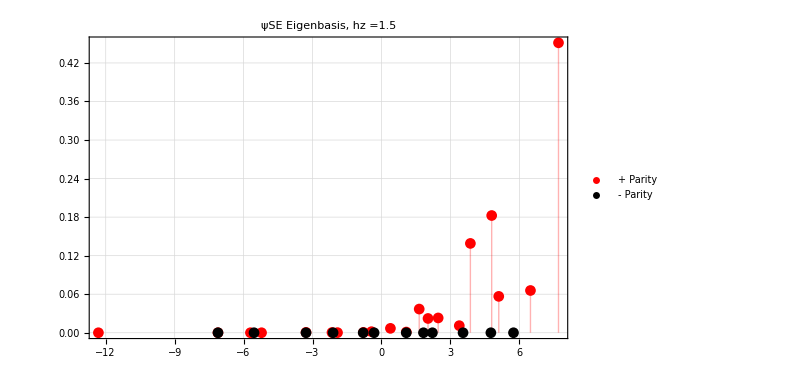

```mathematica
ψ0Espineven=Conjugate[evenEigenVecs].ψ0SE;
ψ0Espinodd=Conjugate[OddEigVecs].ψ0SE;
plota=ListPlot[Abs[ψ0SE]^2,PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Computational basis",25,Black]];
plotb=ListPlot[{Transpose[{EvenEigVals,Abs[ψ0Espineven]^2}],Transpose[{OddEigVals,Abs[ψ0Espinodd]^2}]},PlotRange->All,Filling->Axis,PlotTheme->"Detailed",ImageSize->600,PlotLabel->Style["ψSE Eigenbasis, hz ="<>ToString[hz],25,Black],PlotStyle->{Red,Black},PlotLegends->{Style["+ Parity",20,Red],Style["- Parity",20,Black]}];
Row[{plota,plotb}]
```

## 0<=t<=5

```mathematica
?Superoperator
```

```mathematica
ψT={coherentstate[qubit[RandomReal[],RandomReal[]],L-1],VectorFromKetInComputationalBasis[ConstantArray[1,L-1]],RandomChainProductState[L-1]};
```

```mathematica
styles={Style["Coherent state, h_z = "<>ToString[hz],50,Black],Style["Up state, h_z = "<>ToString[hz],50,Black],Style["Random product state, h_z = "<>ToString[hz],50,Black]};
```

```mathematica
tf=2.0;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]];
,{i,3}]
```

```mathematica
t=1.4;
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
```

```mathematica
Export["test_L_10_h_0.8.png",testimage,ImageSize->4000,ImageResolution->400]
```

test_L_10_h_0.8.png

```mathematica
grids=Table[Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All],{t,0,tf,0.1}];
```

```mathematica
Table[Export["h_z_"<>ToString[hz]<>"_frame_"<>ToString[i]<>".png",grids[[i]],ImageSize->1000,ImageResolution->300],{i,3}]
```

{h_z_1.5_frame_1.png,h_z_1.5_frame_2.png,h_z_1.5_frame_3.png}

# Quantum map for LMG

The model is literally a copy paste version of a spin chain, the only addition is that the interaction term is all to all in pairs. For very particular initial states of the chaometer and environment, one could take advantage of the symmetry of this model but those will impose very hard restriction on the construction for the quantum channel.

So, basically the LMG Hamiltonian is an spin Hamiltonian with all to all interaction terms, and we do not have to worry about the initial total state. Depending on the results we get, could be beneficial or not, to analyse the partition of the total Hilbert space as a direct sum of (very highly) degenerate subspaces of constant angular momentum of the spin chain (coming from the addition of the individual s=1/2).

H_LMG = α(1/2) ∑_(i=1)^N σ_z^(i) + β/N(1/4) ∑_(i=1)^N ∑_(j=1)^N σ_x^(i)σ_x^(j)

ChatGPT already knows 😏 how to write down the Hamiltonian, I have only added some constants for the definition of the collective spin angular momentum operators. The value of N (number of spins) in the second term is for consistency if we were interested in the scaling behavior of some quantities (it can be removed if you wish).

```mathematica
(*Define the Pauli matrices*)
sx={{0,1},{1,0}};
sy={{0,-I},{I,0}};
sz={{1,0},{0,-1}};
(*Define collective spin operators for n spins*)
Clear[Jx,Jy,Jz,n];
Jx[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sx,IdentityMatrix[2]],{j,n}],{i,n}];
Jy[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sy,IdentityMatrix[2]],{j,n}],{i,n}];
Jz[n_]:=(1/2)Sum[KroneckerProduct@@Table[If[j==i,sz,IdentityMatrix[2]],{j,n}],{i,n}];
```

```mathematica
(*Define the Lipkin Hamiltonian*)
Clear[H];
H[α_,β_,n_]:=α*Jz[n]+β/n(Jx[n].Jx[n]);
```

```mathematica
n=L=10;
α=-0.45;
β=3*α;
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[N[H[α,β,n]]]]]];
```

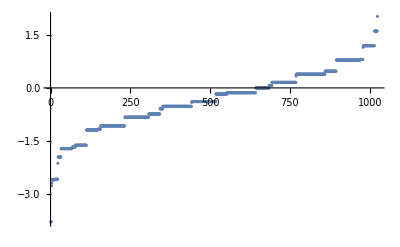

```mathematica
ListPlot[eigenval,PlotRange->All]
```

```mathematica
iprs=Table[Total[Abs[i]^4],{i,eigenvec}];
```

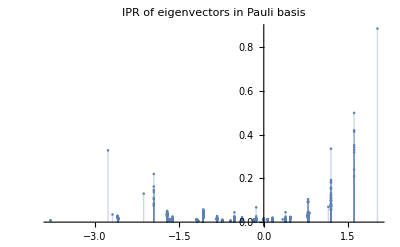

```mathematica
ListPlot[Transpose[{eigenval,iprs}],PlotRange->All,Filling->Axis,PlotLabel->Style["IPR of eigenvectors in Pauli basis", 20,Black]]
```

## Quantum map

From here, everything is a complete copy of what we’ve being doing so far...

```mathematica
(*Set parameters in integrable region and compute Hamiltonian, and its eigenvalues and eigenvectors*)
(*number of spins*)
Clear[n,Ham];
n=L=9;
α=-0.45;
β=3*α;
```

```mathematica
Ham=N[H[α,β,n]];
{eigVals,eigVecs}=Transpose[Sort[Transpose[Eigensystem[Ham]]]];
```

```mathematica
ψT={coherentstate[qubit[Pi,2Pi],L-1],coherentstate[qubit[RandomReal[],RandomReal[]],L-1],RandomChainProductState[L-1]};
```

```mathematica
styles={Style["Coherent state (1,1), α = "<>ToString[α]<>", β = "<>ToString[β],40,Black],Style["Random coherent state, α = "<>ToString[α]<>", β = "<>ToString[β],40,Black],Style["Random product state, α = "<>ToString[α]<>", β = "<>ToString[β],40,Black]};
```

```mathematica
tf=2.0;
```

```mathematica
(*For each initial state compute bloch sphere dynamics and export it as video*)
figs={};
listplots={};
Do[
AppendTo[figs,{}];
choiEigenvalues={};
Do[
superOp=Superoperator[t,ψT[[i]],eigVals,eigVecs,L];
f[x_,y_,z_]:=BlochVector[ArrayReshape[superOp.{1+z,x-ⅈ y,x+ⅈ y,1-z}/2,{2,2}]];
AppendTo[figs[[i]],
Graphics3D[{{Opacity[0.2],Sphere[]},
{Arrow[{{0,0,0},{0,0,1}}],Arrow[{{0,0,0},{0,1,0}}],Arrow[{{0,0,0},{1,0,0}}]},
Opacity[0.75],GrayLevel[.4],
Flatten[Table[Point[f@@{Sin[θ]Cos[ϕ],Sin[θ]Sin[ϕ],Cos[θ]}],{θ,0,Pi,Pi/30},{ϕ,0,2Pi,Pi/30}]],
{Red,PointSize[0.03],Point[f@@{0,0,1}]},
{Green,PointSize[0.03],Point[f@@{0,0,-1}]},
{Orange,PointSize[0.03],Point[f@@{0,1,0}]},
{Cyan,PointSize[0.03],Point[f@@{0,-1,0}]},
{Magenta,PointSize[0.03],Point[f@@{1,0,0}]},
{Blue,PointSize[0.03],Point[f@@{-1,0,0}]}
},
PlotLabel->"t = "<>ToString[t],
Axes->True,Ticks->None,AxesLabel->{x,y,z},
LabelStyle->Directive[Black,FontSize->22,FontFamily->"Arial"],
ViewPoint->{Pi,Pi/2,2},ImageSize->800
]
];
AppendTo[choiEigenvalues,
Transpose[{ConstantArray[t,4],Eigenvalues[1/2.Reshuffle[superOp]]}]
];,{t,0,tf,.1}];
AppendTo[listplots,
ListPlot[Transpose[Chop[choiEigenvalues]],
(*Epilog->{Dynamic[Red,Line[{{t,0},{t,1}}]]},*)
Joined->True,
PlotStyle->Directive[Dashed],
PlotMarkers->{Automatic,Scaled[0.03]},
PlotRange->All,
Frame->True,
FrameStyle->Directive[Black,FontSize->20],
FrameLabel->{"StyleBox[\"t\",FontSlant->\"Italic\"]","eigenvalues( Choi )"},
GridLines->Automatic,
GridLinesStyle->Directive[Dashed,LightGray],
ImageSize->800,PlotLabel->styles[[i]]]];
,{i,3}]
```

```mathematica
t=0.5;
testimage=Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All];
```

```mathematica
Export["test_n_"<>ToString[n]<>"_alfa_"<>ToString[α]<>"_beta_"<>ToString[β]<>".png",testimage,ImageSize->4000]
```

test_n_9_alfa_0.45_beta_1.35.png

```mathematica
grids=Table[Grid[Table[{Show[listplots[[i]],Epilog->{Red,Line[{{t,-1},{t,2}}]}],figs[[i,Round[t*10]+1]]},{i,3}],Spacings->{5,5},Alignment->{Center,Center},Frame->All],{t,0,tf,0.1}];
```

```mathematica
Table[Export["alfa_"<>ToString[α]<>"_beta_"<>ToString[β]<>"L_"<>ToString[n]<>"_frame_"<>ToString[i]<>".png",grids[[i]],ImageSize->1000],{i,Length[grids]}]
```

$Aborted